## Grid count convergence

Using 1e5 macroparticles

```mathematica
(*raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2024-10-11-10-58-00.json"];*)
raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2024-10-14-19-53-39.json"];
raw= Association[#]&/@raw;
```

```mathematica
raw[[1]]//Keys
```

{solSet,gridCount,P_emitSI90_x,P_emitSI90_y,PDrive_emitSI90_x,PDrive_emitSI90_y,PWitness_emitSI90_x,PWitness_emitSI90_y,PDrive_charge,PWitness_charge}

```mathematica
raw[[1]]
```

<|solSet→-0.41,gridCount→5.,P_emitSI90_x→0.0000113251,P_emitSI90_y→0.000011492,PDrive_emitSI90_x→5.3184×10^-6,PDrive_emitSI90_y→5.2167×10^-6,PWitness_emitSI90_x→4.858×10^-6,PWitness_emitSI90_y→5.0143×10^-6,PDrive_charge→1.2×10^-9,PWitness_charge→4.×10^-10|>

```mathematica
driveData = {#"gridCount",10^6#"PDrive_emitSI90_x"}&/@raw;
witnessData={#"gridCount",10^6#"PWitness_emitSI90_x"}&/@raw;
projectedData={#"gridCount",10^6#"P_emitSI90_x"}&/@raw;

allData = {driveData,witnessData,projectedData};
```

```mathematica
expr = a + b x + c x^2;
{driveNLM,witnessNLM,projectedNLM} =NonlinearModelFit[
#,
expr,
{a,b,c},
x
]&/@allData;
```

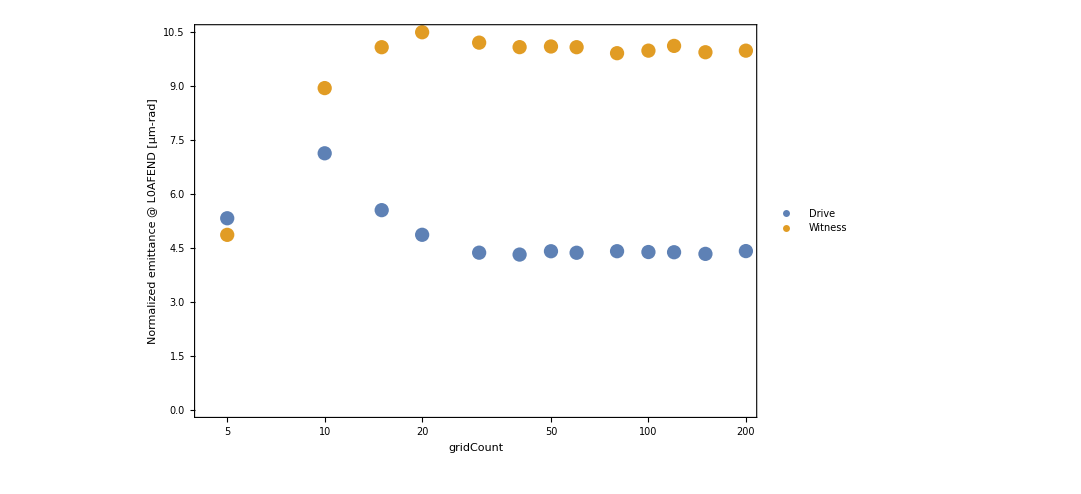

```mathematica
ListLogLinearPlot[
allData[[1;;2]],
PlotLegends->Placed[{"Drive","Witness","Projected"},{0.9,0.1}],
Frame->True,
FrameLabel->{"gridCount","Normalized emittance @ L0AFEND [μm-rad]"},
ImageSize->800,
LabelStyle->20,
PlotRange->{Automatic,Automatic}
]
```

## Solenoid scan

```mathematica
(*raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2024-10-11-10-58-00.json"];*)
raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2024-10-15-09-19-44.json"];
raw= Association[#]&/@raw;
```

```mathematica
raw[[1]]//Keys
```

{solSet,gridCount,P_emitSI90_x,P_emitSI90_y,PDrive_emitSI90_x,PDrive_emitSI90_y,PWitness_emitSI90_x,PWitness_emitSI90_y,PDrive_charge,PWitness_charge}

```mathematica
raw[[1]]
```

<|solSet→-0.35,gridCount→60.,P_emitSI90_x→0.0000111591,P_emitSI90_y→0.0000112072,PDrive_emitSI90_x→8.661×10^-6,PDrive_emitSI90_y→8.6732×10^-6,PWitness_emitSI90_x→5.281×10^-6,PWitness_emitSI90_y→5.2408×10^-6,PDrive_charge→1.2×10^-9,PWitness_charge→4.×10^-10|>

```mathematica
driveData = {-#"solSet",10^6#"PDrive_emitSI90_x"}&/@raw;
witnessData={-#"solSet",10^6#"PWitness_emitSI90_x"}&/@raw;
projectedData={-#"solSet",10^6#"P_emitSI90_x"}&/@raw;

allData = {driveData,witnessData,projectedData};
```

```mathematica
expr = a + b x + c x^2;
{fitMin,fitMax} = {0.37,0.42};
{driveNLM,witnessNLM,projectedNLM} =NonlinearModelFit[
(*#,*)
Select[#,fitMin<=#[[1]]<=fitMax&],
expr,
{a,b,c},
x
]&/@allData;
```

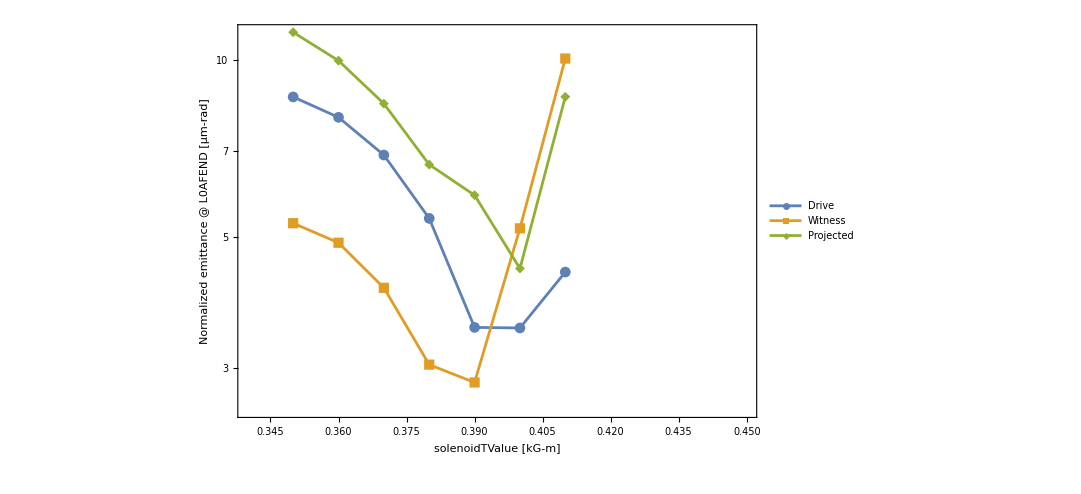

```mathematica
Show[
ListLogPlot[allData,
PlotLegends->Placed[{"Drive","Witness","Projected"},{0.1,0.15}],
Frame->True,
FrameLabel->{Row[{
(*Style["solenoidTValue ",FontFamily->"Courier"], *)
Style["solenoidTValue ",FontFamily->"Fixedsys Excelsior"], 
"[kG-m]"
}],"Normalized emittance @ L0AFEND [μm-rad]"},
ImageSize->800,
LabelStyle->20,
PlotRange->{{0.34,0.45},Automatic},
Joined->True,
PlotMarkers->Automatic
]
(*,
LogPlot[{driveNLM["BestFit"],witnessNLM["BestFit"],projectedNLM["BestFit"]} ,{x,fitMin,fitMax}]*)

]
```